# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Breaking time reversal symmetry

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=Sx[J]=SparseArray[(1/2)(SM[J]+Sm[J])];
Sy[J_]:=Sy[J]=SparseArray[(1/(2I))(SM[J]-Sm[J])];
```

# Method

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

20272

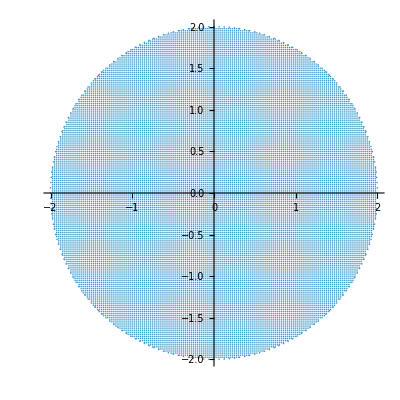

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
(*rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];*)
```

```mathematica
Clear[J];
J=300;
α=0.84;
τ=1;
k=20.;
```

```mathematica
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a1,a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Quiet[Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]]
];
a1[J_Integer,theta_,phi_]:=Module[{mvals=Range[-J,J],coeffs},
Quiet[Normalize[N[Table[Binomial[2J,J+m]*(Cos[theta/2]^(J+m))*(Exp[I*phi]Sin[theta/2])^(J-m),{m,mvals}]]]]
];
```

```mathematica
AbsoluteTiming[coherentstates=Developer`ToPackedArray[ParallelTable[a2[J,i[[1]],i[[2]]],{i,region}]];]
```

{247.167,Null}

```mathematica
flist={};
Do[

mat=Floq[J,α,k,τ];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
AppendTo[flist,neweigenvec];
,{k,10,20,0.5}];
```

```mathematica
klist=Table[i,{i,10,20,0.5}];
```

```mathematica
Clear[iprvectorized];
iprvectorized[eigenvec_,states_]:=Module[{overlaps},
overlaps=Conjugate[eigenvec].Transpose[states];
Total[Abs[overlaps]^4,{1}]
];
```

```mathematica
AbsoluteTiming[iprdata=ParallelTable[iprvectorized[i,coherentstates],{i,flist}];]
```

{723.288,Null}

```mathematica
newdata=Table[Transpose[{region[[All,1]],region[[All,2]],iprdata[[i]]}],{i,Length[flist]}];
```

```mathematica
Export["ipr_J_300_alfa_0.84_kmin_10_kmax_20.dat",newdata,"Table"];
```

```mathematica
newdata=Table[-Log[i]/Log[2j+1],{i,data}];plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]],25,Black],ImageSize->500,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
```

```mathematica
plots=Table[

ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]],25,Black],ImageSize->500,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True],{i,Length[flist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

# Full test (correct)

```mathematica
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},Quiet[Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2 J,J+i]]*Exp[(J+i) Log[alfa1]]],{i,-J,J}],20]]]];
```

```mathematica
J=300;
d=2 J+1;
(*Phase space grid*)
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=radius Table[{Cos[i],Sin[i]},{i,0,2 Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
(*Floquet parameters*)
α=0.84;
τ=1.0;
k=15.0;
```

```mathematica
statesOriginal=ParallelMap[a2[J,#[[1]],#[[2]]]&,region];
statesTOriginal=Transpose[statesOriginal];
```

```mathematica
Floq[J_,α_,k_,τ_]:=Module[{Jx,Jy,Jz,d=2 J+1,U1,U2,F},Jx=1/2 (SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m (m+1)],{m,-J,J-1}],{d,d}]+SparseArray[Band[{2,1}]->Table[Sqrt[J (J+1)-m (m+1)],{m,-J,J-1}],{d,d}]);
Jz=DiagonalMatrix[Table[m,{m,-J,J}]];
U1=MatrixExp[-I k Jx.Jx/(2 J)];
U2=MatrixExp[-I α Jz];
U1.U2
];
```

```mathematica
floquet=Floq[J,α,k,τ];
evecs=Orthogonalize[Eigenvectors[floquet]];
```

```mathematica
iprOriginal=Total[Abs[Conjugate[evecs].statesTOriginal]^4,{1}];
```

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprOriginal}],PlotRange->All,PlotLabel->"Original IPR",ImageSize->400,PlotTheme->"Detailed"]
```

```mathematica
a2LogStableCorrect[J_,Q_,P_]:=Module[{mVals,logs,maxLog,terms,norm,α=(Q+I P)/Sqrt[4-(Q^2+P^2)]},
mVals=Range[-J,J];
If[Abs[α]==0,UnitVector[2 J+1,1],
logs=0.5 (LogGamma[2 J+1]-LogGamma[J+1+mVals]-LogGamma[J+1-mVals])+(J+mVals) Log[α];
maxLog=Max[Re[logs]];
terms=Exp[logs-maxLog];
norm=Sqrt[Total[Abs[terms]^2]];
terms/norm]];
```

```mathematica
statesLogStableCorrect=ParallelMap[a2LogStableCorrect[J,#[[1]],#[[2]]]&,region];
```

```mathematica
Norm[statesOriginal[[1]]-statesLogStableCorrect[[1]]]  (*should be~1e-14*)
```

9.51182×10^-15

```mathematica
iprCorrect=Total[Abs[Conjugate[evecs].Transpose[statesLogStableCorrect]]^4,{1}];
```

```mathematica
Max[Abs[iprCorrect-iprOriginal]]  (*should be~0*)
```

7.3986×10^-16

```mathematica
iprOriginalPlot=iprOriginal;
iprLogStablePlot=iprLogStable;  (*old log-stable,incorrect version*)
iprCorrectPlot=iprCorrect;      (*new fixed version*)
```

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprOriginalPlot}],PlotRange->All,PlotLabel->"Original IPR",PlotTheme->"Detailed",ImageSize->400]
```

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprCorrectPlot}],PlotRange->All,PlotLabel->"Correct Log-Stable IPR",PlotTheme->"Detailed",ImageSize->400]
```

```mathematica
ClearAll[coherentStateGeneratorStable];
coherentStateGeneratorStable=Compile[{{J,_Integer},{q,_Real},{p,_Real}},
Module[{dim,α,result,mVals,logs,maxLog,terms,norm},
dim=2 J+1;
result=ConstantArray[0.0+0. I,dim];
(*Pre-allocate fixed size complex vector*)
α=(q+I p)/Sqrt[4-(q^2+p^2)];
If[Abs[α]==0,result[[1]]=1.0+0. I,
(*Set only the first component*)
mVals=Range[-J,J];
logs=0.5 (LogGamma[2 J+1]-LogGamma[J+1+mVals]-LogGamma[J+1-mVals])+(J+mVals) Log[α];
maxLog=Max[Re[logs]];
terms=Exp[logs-maxLog];
norm=Sqrt[Total[Abs[terms]^2]];
result=terms/norm;];
result],CompilationTarget->"WVM",RuntimeOptions->"Speed",Parallelization->True,RuntimeAttributes->{Listable}];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
statesCompiled=ParallelMap[coherentStateGeneratorStable[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 8030 points...

```mathematica
overlaps=Conjugate[evecs].Transpose[statesCompiled];  (*shape:{d,Npoints}*)
```

```mathematica
iprCompiled=Total[Abs[overlaps]^4,{1}];  (*shape:{Npoints}*)
```

```mathematica
Print["Computing Floquet matrix..."];
floquet=Floq[J,α,k,τ];
evecs=Orthogonalize[Eigenvectors[floquet]];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[evecs].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
Max[Abs[iprCompiled-iprOriginal]]
```

6.88685×10^-16

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprCompiled}],PlotRange->All,PlotLabel->"IPR (Compiled States)",ImageSize->500,PlotTheme->"Detailed"]
```

```mathematica
(*Phase space grid*)
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=radius Table[{Cos[i],Sin[i]},{i,0,2 Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

31602

```mathematica
(*Parameters*)
J=500;
α=0.84;
τ=1;
(*Step 1:Generate all coherent states ONCE*)
Print["[1] Generating coherent states..."];
statesCompiled=ParallelMap[coherentStateGeneratorStable[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
statesCompiledT=Transpose[statesCompiled];  (*For matrix multiplication*)
```

[1] Generating coherent states...

```mathematica
klist=Table[i,{i,10,20,0.01}];
```

```mathematica
(*Step 2:Loop over k values and compute IPRs*)
Do[
k=klist[[i]];
Print["[2] Computing Floquet matrix for k = ",k,"..."];
floquet=Floq[J,α,k,τ];
evecs=Orthogonalize[Eigenvectors[floquet]];
Print["[3] Projecting states and computing IPR..."];
overlaps=Conjugate[evecs].statesCompiledT;
iprCompiled=Total[Abs[overlaps]^4,{1}];
(*Optional:plot and export*)(*Compute D2 entropy from IPR*)
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
(*Generate plot*)
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True];
(*Export figure*)
Export["d2_k_"<>ToString[NumberForm[k,{4,2}]]<>".png",plot];

,{i,Length[klist]}];
```

```mathematica
k=14.;
floquet=Floq[J,α,k,τ];
evecs=Orthogonalize[Eigenvectors[floquet]];
overlaps=Conjugate[evecs].statesCompiledT;
iprCompiled=Total[Abs[overlaps]^4,{1}];
(*Optional:plot and export*)(*Compute D2 entropy from IPR*)
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprCompiled}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

# Phase space

```mathematica
(*Clear[Floq];
Floq[J_,α_,k_,τ_]:=Module[{Jx,Jy,Jz,d=2 J+1,U1,U2,F},Jx=1/2 (SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m (m+1)],{m,-J,J-1}],{d,d}]+SparseArray[Band[{2,1}]->Table[Sqrt[J (J+1)-m (m+1)],{m,-J,J-1}],{d,d}]);
Jz=DiagonalMatrix[Table[m,{m,-J,J}]];
U1=MatrixExp[-I k Jx.Jx/(2 J)];
U2=MatrixExp[-I α Jz];
U1.U2
];*)
(*Clear all cached/memoized definitions*)
ClearAll[sz,sm,sp,sx,sy,sx2,kickPart,twistPart,Floq];
(*Define Sz operator:diagonal with eigenvalues m=-J to J*)
sz[j_]:=sz[j]=DiagonalMatrix[Table[-j+k-1,{k,1,2 j+1}]];
(*Raising operator S_+(superdiagonal)*)
sp[j_]:=sp[j]=DiagonalMatrix[Table[Sqrt[j (j+1)-m (m+1)],{m,-j,j-1}],1];
(*Lowering operator S_-(subdiagonal)*)
sm[j_]:=sm[j]=DiagonalMatrix[Table[Sqrt[j (j+1)-m (m-1)],{m,-j+1,j}],-1];
(*Sx and Sy from ladder operators,defined as sparse for efficiency*)
sx[j_]:=sx[j]=SparseArray[(1/2) (sp[j]+sm[j])];
sy[j_]:=sy[j]=SparseArray[(1/(2 I)) (sp[j]-sm[j])];
(*Precompute Sx^2 for each J only once*)
sx2[j_]:=sx2[j]=sx[j].sx[j];
(*Matrix exponential of the nonlinear "kick" part:exp(-i k/(2J) Sx^2)*)
kickPart[j_,k_]:=kickPart[j,k]=MatrixExp[(-I*k/(2 j)) sx2[j]];
(*Matrix exponential of the linear "twist" part:exp(-i α τ Sz)*)
twistPart[j_,α_,τ_]:=MatrixExp[(-I*α*τ) sz[j]];
(*Final Floquet operator:U=kick.twist*)
Floq[j_,α_,k_,τ_]:=kickPart[j,k].twistPart[j,α,τ];
ClearAll[coherentStateGeneratorStable];
coherentStateGeneratorStable=Compile[{{J,_Integer},{q,_Real},{p,_Real}},
Module[{dim,α,result,mVals,logs,maxLog,terms,norm},
dim=2 J+1;
result=ConstantArray[0.0+0. I,dim];
(*Pre-allocate fixed size complex vector*)
α=(q+I p)/Sqrt[4-(q^2+p^2)];
If[Abs[α]==0,result[[1]]=1.0+0. I,
(*Set only the first component*)
mVals=Range[-J,J];
logs=0.5 (LogGamma[2 J+1]-LogGamma[J+1+mVals]-LogGamma[J+1-mVals])+(J+mVals) Log[α];
maxLog=Max[Re[logs]];
terms=Exp[logs-maxLog];
norm=Sqrt[Total[Abs[terms]^2]];
result=terms/norm;];
result],CompilationTarget->"WVM",RuntimeOptions->"Speed",Parallelization->True,RuntimeAttributes->{Listable}];
```

```mathematica
(*(*Phase space grid*)
radius=1.99999;
delta=0.010;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=radius Table[{Cos[i],Sin[i]},{i,0,2 Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region=circlePoints;*)
```

```mathematica
radius=1.99999;
delta=0.0100;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
```

```mathematica
xCoords=Range[0,radius,delta];
yCoords=Range[0,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
gridPointsQuarter=Select[gridPointsRaw,Norm[#]<radius&];
```

```mathematica
gridPointsQuarter//Dimensions
```

{31602,2}

```mathematica
(*Floquet parameters*)
J=500;
d=2 J+1;
α=1.31;
τ=1.0;
k=20.0;
```

```mathematica
θSector=α/2;  (*Symmetry wedge orientation*)
rotation[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
regionQuarter=rotation[θSector].#&/@gridPointsQuarter;
```

```mathematica
(*ListPlot[regionQuarter,AspectRatio->1,PlotRange->{{-2,2},{-2,2}}]*)
```

```mathematica
Print["Generating coherent states over ",Length[regionQuarter]," points..."];
statesCompiled=ParallelMap[coherentStateGeneratorStable[J,#[[1]],#[[2]]]&,regionQuarter,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31602 points...

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k,τ];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

Computing Floquet matrix...

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
ListDensityPlot[Transpose[{regionQuarter[[All,1]],regionQuarter[[All,2]],iprCompiled}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
(*Generate plot*)
plot=ListDensityPlot[Transpose[{regionQuarter[[All,1]],regionQuarter[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
rotation[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
reflectPoint[p_,θ_]:=Module[{R=rotation[θ]},R.DiagonalMatrix[{1,-1}].Transpose[R].p];
```

```mathematica
(*Reflect regions*)
θ1=α/2;
θ2=θ1+π/2;
reflect1[p_]:=reflectPoint[p,θ1];
reflect2[p_]:=reflectPoint[p,θ2];
reflectBoth[p_]:=reflect1[reflect2[p]];
region1=regionQuarter;
region2=reflect1/@regionQuarter;
region3=reflect2/@regionQuarter;
region4=reflectBoth/@regionQuarter;
fullRegion=Join[region1,region2,region3,region4];
```

```mathematica
(*Reflect data:values remain the same*)
ipr1=iprCompiled;
ipr2=iprCompiled;
ipr3=iprCompiled;
ipr4=iprCompiled;
fullIPR=Join[ipr1,ipr2,ipr3,ipr4];
```

```mathematica
(*Combine all regions and corresponding IPRs*)
allPoints=Join[region1,region2,region3,region4];
allIPRs=Join[ipr1,ipr2,ipr3,ipr4];
(*Round points to avoid numerical noise (e.g.,1e-16 differences)*)
roundedPoints=Round[allPoints,10^-6];
(*Pair up rounded points and IPRs*)
paired=Transpose[{roundedPoints,allIPRs}];
(*Remove duplicates by point*)
uniquePairs=DeleteDuplicatesBy[paired,First];
(*Unpack back to region and IPR*)
{uniqueRegion,uniqueIPR}=Transpose[uniquePairs];
```

```mathematica
Dimensions[uniqueRegion]
Dimensions[uniqueIPR]
```

{125609,2}

{125609}

```mathematica
ListDensityPlot[Transpose[{uniqueRegion[[All,1]],uniqueRegion[[All,2]],uniqueIPR}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,uniqueIPR}];
```

```mathematica
(*Generate plot*)
plot=ListDensityPlot[Transpose[{uniqueRegion[[All,1]],uniqueRegion[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

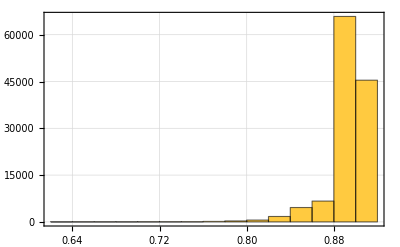

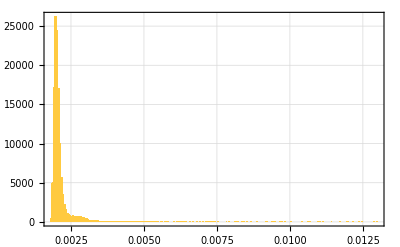

```mathematica
Histogram[newdata,PlotRange->All,PlotTheme->"Detailed"]
Histogram[uniqueIPR,PlotRange->All,PlotTheme->"Detailed"]
```

## Cycle (verify)

```mathematica
alist=Table[i,{i,0.,2.Pi,Pi/50}];
```

```mathematica
(*Step 2:Loop over k values and compute IPRs*)
Do[
α=alist[[i]];
Print["[2] Computing Floquet matrix for α = ",α,"..."];

mat=Floq[J,α,k,τ];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
(*Reflect regions*)
θ1=α/2;
θ2=θ1+π/2;
reflect1[p_]:=reflectPoint[p,θ1];
reflect2[p_]:=reflectPoint[p,θ2];
reflectBoth[p_]:=reflect1[reflect2[p]];
region1=regionQuarter;
region2=reflect1/@regionQuarter;
region3=reflect2/@regionQuarter;
region4=reflectBoth/@regionQuarter;
(*Reflect data:values remain the same*)
ipr1=iprCompiled;
ipr2=iprCompiled;
ipr3=iprCompiled;
ipr4=iprCompiled;
(*Combine all regions and corresponding IPRs*)
allPoints=Join[region1,region2,region3,region4];
allIPRs=Join[ipr1,ipr2,ipr3,ipr4];
(*Round points to avoid numerical noise (e.g.,1e-16 differences)*)
roundedPoints=Round[allPoints,10^-6];
(*Pair up rounded points and IPRs*)
paired=Transpose[{roundedPoints,allIPRs}];
(*Remove duplicates by point*)
uniquePairs=DeleteDuplicatesBy[paired,First];
(*Unpack back to region and IPR*)
{uniqueRegion,uniqueIPR}=Transpose[uniquePairs];
(*Optional:plot and export*)(*Compute D2 entropy from IPR*)
newdata=Table[-Log[i]/Log[2 J+1],{i,uniqueIPR}];
(*Generate plot*)
plot=ListDensityPlot[Transpose[{uniqueRegion[[All,1]],uniqueRegion[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True];
(*Export figure*)
Export["d2_k_"<>ToString[NumberForm[α,{4,2}]]<>".png",plot];

,{i,Length[alist]}];
```

[2] Computing Floquet matrix for α = 0....

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.0628319...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.125664...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.188496...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.251327...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.314159...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.376991...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.439823...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.502655...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.565487...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.628319...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.69115...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.753982...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.816814...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.879646...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 0.942478...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.00531...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.06814...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.13097...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.19381...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.25664...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.31947...

Projecting states into Floquet basis...

Computing IPRs...

[2] Computing Floquet matrix for α = 1.3823...

Projecting states into Floquet basis...

$Aborted

# Phase space measure tests

```mathematica
Clear[Floq];
Floq[J_,α_,k_,τ_]:=Module[{Jx,Jy,Jz,d=2 J+1,U1,U2,F},Jx=1/2 (SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m (m+1)],{m,-J,J-1}],{d,d}]+SparseArray[Band[{2,1}]->Table[Sqrt[J (J+1)-m (m+1)],{m,-J,J-1}],{d,d}]);
Jz=DiagonalMatrix[Table[m,{m,-J,J}]];
U1=MatrixExp[-I k Jx.Jx/(2 J)];
U2=MatrixExp[-I α Jz];
U1.U2
];
ClearAll[coherentStateGeneratorStable];
coherentStateGeneratorStable=Compile[{{J,_Integer},{q,_Real},{p,_Real}},
Module[{dim,α,result,mVals,logs,maxLog,terms,norm},
dim=2 J+1;
result=ConstantArray[0.0+0. I,dim];
(*Pre-allocate fixed size complex vector*)
α=(q+I p)/Sqrt[4-(q^2+p^2)];
If[Abs[α]==0,result[[1]]=1.0+0. I,
(*Set only the first component*)
mVals=Range[-J,J];
logs=0.5 (LogGamma[2 J+1]-LogGamma[J+1+mVals]-LogGamma[J+1-mVals])+(J+mVals) Log[α];
maxLog=Max[Re[logs]];
terms=Exp[logs-maxLog];
norm=Sqrt[Total[Abs[terms]^2]];
result=terms/norm;];
result],CompilationTarget->"WVM",RuntimeOptions->"Speed",Parallelization->True,RuntimeAttributes->{Listable}];
```

```mathematica
J=200;
d=2 J+1;
(*Phase space grid*)
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=radius Table[{Cos[i],Sin[i]},{i,0,2 Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region=circlePoints;
(*Floquet parameters*)
α=0.84;
τ=1.0;
k=1.3;
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
statesCompiled=ParallelMap[coherentStateGeneratorStable[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31401 points...

```mathematica
Print["Computing Floquet matrix..."];
Clear[floquet];
floquet=Floq[J,α,k,τ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[floquet]]]];
evecs=Orthogonalize[eigenvec];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[evecs].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprCompiled}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
(*---Minimal Husimi normalization test on your existing rectangular grid---*)(*Assumes you already have:J,delta,circlePoints  (*ONLY interior points*),statesCompiled          (* |Ω(Q,P)>at those points,in m=-J..J basis*),and evecs               (*Floquet eigenvectors as length-(2J+1) vectors*).*)
dim=2 J+1;
pref=(2 J+1)/(4 Pi);
ΔA=delta^2;
(*Geometric correction so the integral of 1 is exact on your grid*)
Atrue=4 Pi;                                   (*area of disk radius 2*)
Aest=ΔA*Length[circlePoints];              (*area represented by midpoints*)
c=Atrue/Aest;                             (* ≈1.00175 in your run*)
(*Build ⟨Ω|as rows once*)
Sbra=Conjugate[statesCompiled];               (*(#points)×dim*)
```

```mathematica
(*Husimi and normalization*)
husimiFor[ψ_]:=Abs[Sbra.ψ]^2;               (*length=#points*)
normalizeRect[ψ_]:=pref*(c*ΔA)*Total[husimiFor[ψ]];
```

```mathematica
Svals=normalizeRect/@evecs;
```

```mathematica
err=Svals-1.0;
<|"MeanError"->Mean[err],"MaxAbsError"->Max[Abs[err]],"MinS"->Min[Svals],"MaxS"->Max[Svals],"Check_Constant"->pref*(c*ΔA)*Length[circlePoints]  (*should be≈2J+1*)|>
```

<|MeanError→-4.09758×10^-17,MaxAbsError→0.0362954,MinS→0.963705,MaxS→1.0025,Check_Constant→401.|>

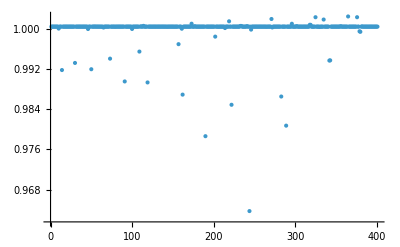

```mathematica
ListPlot[Svals,PlotRange->All]
```

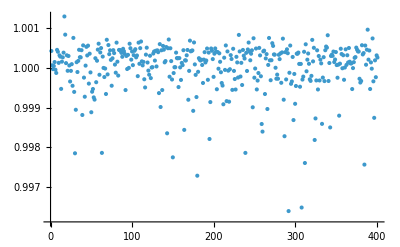

```mathematica
ListPlot[Svals,PlotRange->All]
```

```mathematica
(* ===Localization measures on your (Q,P) grid:intrinsic only===*)(*Assumes:J,delta,circlePoints,statesCompiled,evecs,pref=(2 J+1)/(4 Pi),ΔA=delta^2,c=(4 Pi)/(ΔA Length[circlePoints]),Sbra=Conjugate[statesCompiled].*)(*1) Husimi values for all eigenvectors at all grid points*)
V=Transpose[evecs];                 (*(2J+1) x dim*)
H=Abs[Sbra.V]^2;                               (*(#points) x dim*)

(*2) Normalization check per eigenvector (should be≈1)*)
Snorm=pref*(c*ΔA)*Total[H,{1}];              (*length dim*)

(*3) Wehrl entropy S_W (natural log)*)
eps=$MachineEpsilon;
Hcl=Clip[H,{eps,Infinity}];
SW=-pref*(c*ΔA)*Total[Hcl*Log[Hcl],{1}];

(*4) Rényi-2/IPR-based measures*)
I2=pref*(c*ΔA)*Total[H^2,{1}];           (*Husimi IPR*)
S2=-Log[I2];
Neff=Exp[S2];                                       (*effective # of cells*)
Fsup=Neff/(2 J+1.0);                              (*fractional support in[0,1]*)

(*5) Optional intrinsic scaling for Wehrl (no ensembles)*)
Smin=2.0 J/(2.0 J+1.0);                           (*SU(2) Wehrl minimum*)
LW=(SW-Smin)/(Log[2.0 J+1.0]-Smin);
```

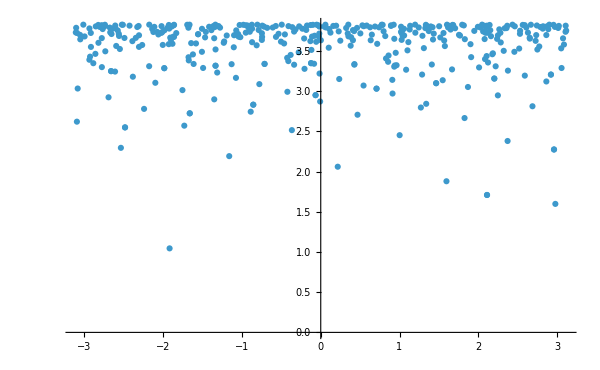

```mathematica
ListPlot[Transpose[{Arg[eigenval],SW}],PlotRange->All,ImageSize->600]
```

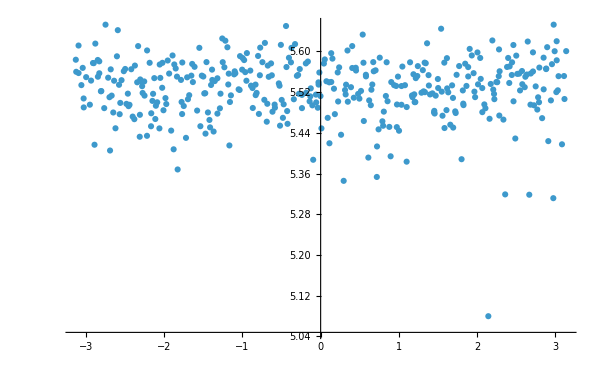

```mathematica
ListPlot[Transpose[{Arg[eigenval],SW}],PlotRange->All,ImageSize->600]
```

# Four parity sectors S (all wrong)

```mathematica
Clear[Sz,Sz,U];
Sz[J_]:=DiagonalMatrix[Range[-J,J]];
Sx[J_]:=1/2 (SparseArray[Band[{1,2}]->Table[Sqrt[J(J+1)-m(m+1)],{m,-J,J-1}],{2J+1,2J+1}]+SparseArray[Band[{2,1}]->Table[Sqrt[J(J+1)-m(m-1)],{m,-J+1,J}],{2J+1,2J+1}]);
(*Symmetry operators*)
P[J_]:=MatrixExp[-I Pi Sz[J]];                (*parity=R_z(pi)*)
Sop[J_]:=MatrixExp[-I (Pi/2) Sz[J]];
```

```mathematica
(*sector indices as before*)
sectorIndices[J_]:=Module[{m=Range[-J,J],r},r=Mod[m,4];
<|"λ=+1"->Flatten@Position[r,0],"λ=-i"->Flatten@Position[r,1],"λ=-1"->Flatten@Position[r,2],"λ=+i"->Flatten@Position[r,3]|>];
(*build Floquet as before*)
U[J_,k_,α_]:=MatrixExp[-I (k/(2 J)) (Sx[J].Sx[J])].MatrixExp[-I α Sz[J]];
(*return an Association:label->block*)
blockDiagonalizeByS[J_,k_,α_]:=Module[{Ufull=U[J,k,α],idx},idx=sectorIndices[J];
Map[Ufull[[#,#]]&,idx]  (*Map over values of the Association,preserving keys*)];
```

```mathematica
J=1000;
k=20.;
α=Pi/2;
blocks=blockDiagonalizeByS[J,k,α];
```

```mathematica
(*Diagonalize each block,preserving keys*)
spec=Map[Eigensystem/*N,blocks];
```

```mathematica
(*If you want eigenvalues and eigenvectors split,still keyed by sector*)
evals=Map[First,spec];
evecs=Map[Last,spec];
```

```mathematica
(*sector sizes*)
KeyValueMap[#1->Length[#2]&,sectorIndices[J]]
(*block sizes*)
KeyValueMap[#1->Dimensions[#2]&,blocks]
(*verify symmetry:blocks commute with U*)
KeyValueMap[#1->Norm[#2.#-#.#2,"Frobenius"]&,blocks]/. #->U[J,k,α]&
```

{λ=+1→501,λ=-i→500,λ=-1→500,λ=+i→500}

{λ=+1→{501,501},λ=-i→{500,500},λ=-1→{500,500},λ=+i→{500,500}}

KeyValueMap[#1→#2.#1-#1.#2&,blocks]/.#1→U[J,k,α]&

```mathematica
(*1) Choose a deterministic sector order*)
order={"λ=+1","λ=-i","λ=-1","λ=+i"}~Intersection~Keys[evals]
```

{λ=-1,λ=+1,λ=-i,λ=+i}

```mathematica
(*2) Build embedding for each sector*)
Ndim=2 J+1;
idxAssoc=sectorIndices[J];
embedMat[ii_List]:=Module[{len=Length[ii],rules},rules=MapThread[({#1,#2}->1)&,{ii,Range[len]}];
SparseArray[rules,{Ndim,len}]];
```

```mathematica
(*Gather eigenvalues in the same sector order you used for the vectors*)
allEigenvalues=Join@@(evals/@order);
(*3) Embed and concatenate*)
vecsList=MapThread[Function[{lab,vraw},With[{V=If[MatrixQ[vraw],vraw,Transpose[vraw]]},
Normal[embedMat[idxAssoc[lab]]].V ]],{order,evecs/@order}];
(*concatenate columns from all sectors,then make ROWS=eigenvectors*)
allEigenvectorsRows=Transpose@Fold[Join[#1,#2,2]&,First@vecsList,Rest@vecsList];
(*Optional:sort by quasienergy phase and reorder ROWS accordingly*)
ord=Ordering[Arg[allEigenvalues]];
alleigenvalues=allEigenvalues[[ord]];
alleigenvectors=allEigenvectorsRows[[ord]];
```

```mathematica
(*Quick sanity checks*)
{Length[alleigenvalues],Dimensions[alleigenvectors]}  (* ->{2 J+1,{2 J+1,2 J+1}}*)
```

{2001,{2001,2001}}

```mathematica
Clear[MeanLevelSpacingRatio];
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
ratiosa=Table[MeanLevelSpacingRatio[Sort[Arg[i]]],{i,evals}]
```

{0.388515,0.379863,0.380278,0.378697}

```mathematica
neweigenval=Join[eigenvalM,eigenvalm];
```

```mathematica
MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]]
MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]
```

0.538561

0.533296